```mathematica
taz=0;
tp=0.003;
tpp=0.004;
tmp=0.004;
tk=0;
tkb=0;
tpppz=0.016;
tmppz=0.016;
tpkp=0.016;
tmkp=-0.016;
μaz=-0.1-6*taz;
μaa=0.11-4(tk+tkb);
μdw=0.11-4(tk+tkb);
A=0.110;
b=0.033;
c=0.033;
d=0.573;
g=π/8;
te=ⅈ;
AA[px_,py_,a_]:=te*Exp[-ⅈ*g](1+ϕ1[px,py,a,1]+ϕ2[px,py,a,-1]);
AA1[px_,py_,a_]:=Conjugate[AA[px,py,a]]
ϕ1[px_,py_,a_,l_]:=Exp[-ⅈ*l*(√3)/2 a(-px+√3 py)]
ϕ2[px_,py_,a_,l_]:=Exp[-ⅈ*l*(√3)/2 a(px+√3 py)]
ϕ3[px_,py_,a_,l_]:=Exp[-ⅈ*l*3a*py]
W[l_]:=Exp[ⅈ*l*(2*π)/3]
ξ[l_]:=Exp[ⅈ*l*(2*π)/6]
H1[px_,py_,a_]:=(ϕ2[px,py,a,1]+ϕ3[px,py,a,1]+ϕ1[px,py,a,1]+ϕ2[px,py,a,-1]+ϕ3[px,py,a,-1]+ϕ1[px,py,a,-1])
R1[px_,py_,a_]:={0,0,0,0,0,0,-(W[1]+ϕ3[px,py,a,1]*W[-1]+ϕ1[px,py,a,1])ξ[-1]*A,(1+ϕ3[px,py,a,1]*W[-1]+ϕ1[px,py,a,1]*W[1])ξ[-1]*A,(W[1]+ϕ2[px,py,a,1]*W[-1]+ϕ3[px,py,a,1])ξ[1]*A,-(W[1]+ϕ2[px,py,a,1]+ϕ3[px,py,a,1]*W[-1])ξ[1]*A}
R2[px_,py_,a_]:={0,0,0,0,0,0,(W[-1]+ϕ3[px,py,a,1]*W[1]+ϕ1[px,py,a,1])ξ[1]*b,(1+ϕ3[px,py,a,1]+ϕ1[px,py,a,1])c,(W[-1]+ϕ2[px,py,a,1]*W[1]+ϕ3[px,py,a,1])ξ[-1]*b,(1+ϕ2[px,py,a,1]+ϕ3[px,py,a,1])c}
R3[px_,py_,a_]:={0,0,0,0,0,0,(1+ϕ3[px,py,a,1]+ϕ1[px,py,a,1])c,(1+ϕ3[px,py,a,1]*W[1]+ϕ1[px,py,a,1]*W[-1])ξ[1]*b,(1+ϕ2[px,py,a,1]+ϕ3[px,py,a,1])c,(W[-1]+ϕ2[px,py,a,1]+ϕ3[px,py,a,1]*W[1])ξ[-1]*b}
R4[px_,py_,a_]:={0,0,0,0,0,0,-ⅈ*d*ϕ2[px,py,a,-1],-ⅈ*d*ϕ2[px,py,a,-1],ⅈ*d,ⅈ*d}
R5[px_,py_,a_]:={0,0,0,0,0,0,-ⅈ*d*W[1],-ⅈ*d*W[-1],ⅈ*d*W[1],ⅈ*d*W[-1]}
R6[px_,py_,a_]:={0,0,0,0,0,0,-ⅈ*W[-1]*d*ϕ1[px,py,a,1],-ⅈ*W[1]*d*ϕ1[px,py,a,1],ⅈ*W[-1]*d,ⅈ*W[1]*d}
R7[px_,py_,a_]:={-(W[-1]+ϕ3[px,py,a,-1]*W[1]+ϕ1[px,py,a,-1])ξ[1]A,(W[1]+ϕ3[px,py,a,-1]*W[-1]+ϕ1[px,py,a,-1])b*ξ[-1],(1+ϕ3[px,py,a,-1]+ϕ1[px,py,a,-1])c,ⅈ*d*ϕ2[px,py,a,1],ⅈ*W[-1]*d,ⅈ*W[1]*d*ϕ1[px,py,a,-1],0,0,0,0}
R8[px_,py_,a_]:={(1+ϕ3[px,py,a,-1]*W[1]+ϕ1[px,py,a,-1]*W[-1])ξ[1]A,(1+ϕ3[px,py,a,-1]+ϕ1[px,py,a,-1])c,(1+W[-1]*ϕ3[px,py,a,-1]+W[1]*ϕ1[px,py,a,-1])ξ[-1]*b,ⅈ*d*ϕ2[px,py,a,1],ⅈ*W[1]*d,ⅈ*W[-1]*d*ϕ1[px,py,a,-1],0,0,0,0}
R9[px_,py_,a_]:={(W[-1]+ϕ2[px,py,a,-1]*W[1]+ϕ3[px,py,a,-1])ξ[-1]A,(W[1]+ϕ2[px,py,a,-1]*W[-1]+ϕ3[px,py,a,-1])b*ξ[1],(1+ϕ2[px,py,a,-1]+ϕ3[px,py,a,-1])c,-ⅈ*d,-ⅈ*W[-1]*d,-ⅈ*W[1]*d,0,0,0,0}
R10[px_,py_,a_]:={-(W[-1]+ϕ2[px,py,a,-1]+ϕ3[px,py,a,-1]*W[1])ξ[-1]A,(1+ϕ2[px,py,a,-1]+ϕ3[px,py,a,-1])c,(W[1]+ϕ2[px,py,a,-1]+ϕ3[px,py,a,-1]*W[-1])b*ξ[1],-ⅈ*d,-ⅈ*W[1]*d,-ⅈ*W[-1]*d,0,0,0,0}
r1[px_,py_,a_]:={μaz,(-ⅈ*tpppz(ϕ1[px,py,a,-1]+ϕ3[px,py,a,1]*W[-1]+ϕ2[px,py,a,-1]W[1])-(-1)ⅈ*tmppz(ϕ1[px,py,a,1]+ϕ3[px,py,a,-1]*W[-1]+ϕ2[px,py,a,1]W[1])),(-(-1)ⅈ*tpppz(ϕ1[px,py,a,1]+ϕ3[px,py,a,-1]*W[1]+ϕ2[px,py,a,1]W[-1])-(-1)(-1)ⅈ*tmppz(ϕ1[px,py,a,-1]+ϕ3[px,py,a,1]*W[1]+ϕ2[px,py,a,-1]W[-1])),0,0,0,0,0,0,0}
r2[px_,py_,a_]:={(ⅈ*tpppz(ϕ1[px,py,a,1]+ϕ3[px,py,a,-1]*W[1]+ϕ2[px,py,a,1]W[-1])-ⅈ*tmppz(ϕ1[px,py,a,-1]+ϕ3[px,py,a,1]*W[1]+ϕ2[px,py,a,-1]W[-1])),tp*H1[px,py,a]+μaa,tpp(ϕ1[px,py,a,-1]+ϕ3[px,py,a,1]W[-1]+ϕ2[px,py,a,-1]W[1])+tmp(ϕ1[px,py,a,1]+ϕ3[px,py,a,-1]W[-1]+ϕ2[px,py,a,1]W[1]),tpkp*ϕ2[px,py,a,1]-tmkp*ϕ3[px,py,a,1],tpkp*ϕ3[px,py,a,1]*W[1]-tmkp*W[1],tpkp*W[-1]-tmkp*ϕ2[px,py,a,1]*W[-1],0,0,0,0}
r3[px_,py_,a_]:={(-ⅈ*tpppz(ϕ1[px,py,a,-1]+ϕ3[px,py,a,1]*W[-1]+ϕ2[px,py,a,-1]W[1])-(-1)ⅈ*tmppz(ϕ1[px,py,a,1]+ϕ3[px,py,a,-1]*W[-1]+ϕ2[px,py,a,1]W[1])),tpp(ϕ1[px,py,a,1]+ϕ3[px,py,a,-1]W[1]+ϕ2[px,py,a,1]W[-1])+tmp(ϕ1[px,py,a,-1]+ϕ3[px,py,a,1]W[1]+ϕ2[px,py,a,-1]W[-1]),tp*H1[px,py,a]+μaa,tpkp*ϕ3[px,py,a,1]-tmkp*ϕ2[px,py,a,1],tpkp*W[-1]-tmkp*ϕ3[px,py,a,1]*W[-1],tpkp*ϕ2[px,py,a,1]*W[1]-tmkp*W[1],0,0,0,0}
r4[px_,py_,a_]:={0,tpkp*ϕ2[px,py,a,-1]-tmkp*ϕ3[px,py,a,-1],tpkp*ϕ3[px,py,a,-1]-tmkp*ϕ2[px,py,a,-1],μdw,0,0,0,0,0,0}
r5[px_,py_,a_]:={0,tpkp*ϕ3[px,py,a,-1]*W[-1]-tmkp*W[-1],tpkp*W[1]-tmkp*ϕ3[px,py,a,-1]*W[1],0,μdw,0,0,0,0,0}
r6[px_,py_,a_]:={0,tpkp*W[1]-tmkp*ϕ2[px,py,a,-1]*W[1],tpkp*ϕ2[px,py,a,-1]*W[-1]-tmkp*W[-1],0,0,μdw,0,0,0,0}
r7[px_,py_,a_]:={0,0,0,0,0,0,0,0,AA[px,py,a],0}
r8[px_,py_,a_]:={0,0,0,0,0,0,0,0,0,AA[px,py,a]}
r9[px_,py_,a_]:={0,0,0,0,0,0,AA1[px,py,a],0,0,0}
r10[px_,py_,a_]:={0,0,0,0,0,0,0,AA1[px,py,a],0,0}
hh[px_,py_,a_]:={R1[px,py,a]+r1[px,py,a],R2[px,py,a]+r2[px,py,a],R3[px,py,a]+r3[px,py,a],R4[px,py,a]+r4[px,py,a],R5[px,py,a]+r5[px,py,a],R6[px,py,a]+r6[px,py,a],R7[px,py,a]+r7[px,py,a],R8[px,py,a]+r8[px,py,a],R9[px,py,a]+r9[px,py,a],R10[px,py,a]+r10[px,py,a]}
```

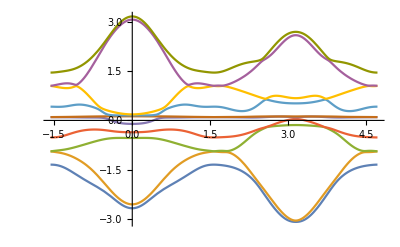

```mathematica
Block[{getEv},getEv[θ_?NumericQ]:=getEv[θ]=Sort@Eigenvalues[hh[Cos[θ],Sin[θ],1.4]];
getEv[θ_?NumericQ,n_]:=getEv[θ][[n]];
Plot[Evaluate@Table[getEv[θ,n],{n,10}],{θ,-0.5 π,1.5 π}]]
```